```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

<<NLSMAlgebra`;   (*Loads the math logic*)
<<NLSMLisp`;     (*Loads the translator& Lisp engine*)
<<NLSMVisuals`;
<<NLSMDriver`;
```

Processing terms into: Report

Full Report saved to: Report/S2p_1.pdf

Full Report saved to: Report/S2p_2.pdf

Full Report saved to: Report/S2p_3.pdf

Full Report saved to: Report/S2p_4.pdf

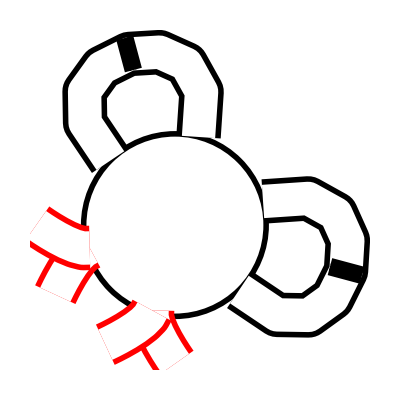
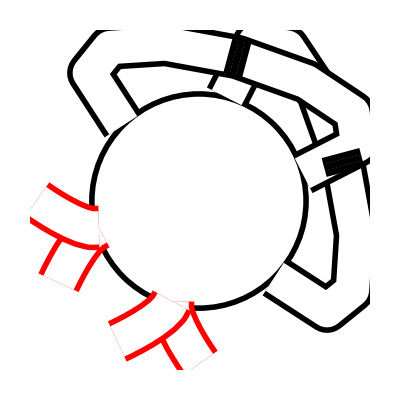
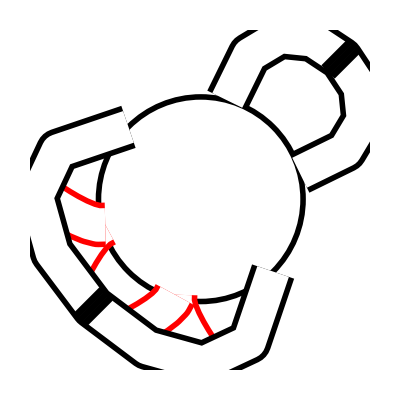
Term 1
Tr[Φ(R).σ_3.W(R).W(R).Φ(R).σ_3.W(R).W(R)]/(2 t) |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | -1/8 t Ð[0]^2 Tr[Perp[Φ[R]].Perp[Φ[R]]]
3 | -Graphics- | 0
____________________
Term 1
Tr[Φ(R).σ_3.W(R).Φ(R).σ_3.W(R).W(R).W(R)]/(2 t) |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
____________________
Term 1
(λ Tr[Φ(R).σ_3.W(R).Φ(R).σ_3.W(R).W(R).W(R)])/(2 t) |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
____________________
Term 1
(λ Tr[Φ(R).σ_3.Φ(R).σ_3.W(R).W(R).W(R).W(R)])/(2 t) |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
____________________

```mathematica
(*2. Define a Dummy Model*)
fullexpr=1/(2 t)Tr[Φ[r].Subscript[σ, 3].W[r].W[r].Φ[r].Subscript[σ, 3].W[r].W[r]]+λ/(2 t)Tr[Φ[r].Subscript[σ, 3].Φ[r].Subscript[σ, 3].W[r].W[r].W[r].W[r]]+(1+λ)/(2 t)Tr[Φ[r].Subscript[σ, 3].W[r].Φ[r].Subscript[σ, 3].W[r].W[r].W[r]];

(*3. Run the Driver*)
NLSMDriver`GenerateDiagrams[fullexpr,"Report","S2p","Display"->True]
```